```mathematica
eqn 1=Dt[M,t]==2π α (G M)^2 V^-3 ρ∞;
```

Adiabatic relation

```mathematica
eqn 2=p/(p∞)==(ρ/(ρ∞))^γ;
```

Equation of continuity

```mathematica
eqn 3=4π r^2 ρ v==A;
```

Bernoulli' s equation

```mathematica
1/2 v^2+Dt[p]/ρ-(G M)/r==0;
```

```mathematica
Dt[p]/ρ;
% /. Solve[eqn 2,p][[1]];
% /. {Dt[p∞]->0,Dt[ρ∞]-> 0,Dt[γ]->0};
%/Dt[ρ];
PowerExpand[%];
Integrate[%,ρ];
%-(%/.ρ-> ρ∞);
Simplify[%];
eqn 5=1/2 v^2+%==(G M)/r;
```

```mathematica
eqn 5
```

v^2/2+(p∞ γ (ρ/(ρ∞)-ρ^γ (ρ∞)^-γ))/(ρ-γ ρ)==(G M)/r

Speed of sound at infinity

```mathematica
eqn 6=c^2==γ p∞/ρ∞;
```

Dimensionless variables

```mathematica
eqn 7={r==x (G M)/c^2,v==y c,ρ==z ρ∞};
```

```mathematica
eqn 10=A==4π λ G^2 M^2 c^-3 ρ∞;
```

```mathematica
eqn 3;
%/.Solve[eqn 7[[1]],r][[1]];
%/. Solve[eqn 7[[2]],v][[1]];
% /. Solve[eqn 7[[3]],ρ][[1]];
% /. Solve[eqn 10,A][[1]];
Simplify[%,{G>0,M>0,c>0,ρ∞>0}];
eqn 8=%;
```

```mathematica
eqn 5;
%/.Solve[eqn 7[[1]],r][[1]];
%/. Solve[eqn 7[[2]],v][[1]];
% /. Solve[eqn 7[[3]],ρ][[1]];
% /. Solve[eqn 6,p∞][[1]];
(%[[1]])/c^2==(%[[2]])/c^2;
PowerExpand[%];
Simplify[%,{c>0}];
eqn 9=%;
```

```mathematica
eqn 9 orig=1/2 y^2+(z^(γ-1)-1)/(γ-1)==1/x;
%/.Solve[eqn 9,x][[1]];
Simplify[%]
```

True

```mathematica
eqn 11=u==y z^(-(γ-1)/2);
```

```mathematica
eqn 8;
%/.Solve[eqn 11,z][[1]];
PowerExpand[%];
eqn 12=%;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
eqn 12 orig=y==u^(2/(γ-1))(λ/x^2)^((γ-1)/(γ+1));
%/.Solve[eqn 12,λ][[1]];
PowerExpand[%];
Simplify[%,y>0]
```

u^(4/(-1+γ^2))==1

Apprently, there' s a mistake in equation 12. The correct form should be

```mathematica
eqn 12 corrected=y==u^(2/(γ+1))(λ/x^2)^((γ-1)/(γ+1));
%/.Solve[eqn 12,λ][[1]];
PowerExpand[%];
Simplify[%,y>0]
```

True

```mathematica
eqn 11;
z/.Solve[%,z][[1]];
% /. Solve[eqn 12,y][[1]];
PowerExpand[%];
Simplify[%];
eqn 13=z==%;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
eqn 9;
% /. Solve[eqn 12,y][[1]];
% /. Solve[eqn 13,z][[1]];
PowerExpand[%];
FullSimplify[%];
eqn 14=%;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
eqn 14 orig=1/2 u^(4/(γ+1))(λ/x^2)^(2(γ-1)/(γ+1))+1/(γ-1)(λ/(x^2 u))^(2(γ-1)/(γ+1))==1/x+1/(γ-1);
(%[[1]]-%[[2]])-(eqn 14[[1]]-eqn 14[[2]]);
PowerExpand[%];
Simplify[%]
```

0

This is strange. Equations 12 & 13 are wrong, but 14 is correct.

```mathematica
eqn 15=f[u]==λ^(-2(γ-1)/(γ+1))g[x];
```

```mathematica
eqn 16=f[u]==1/2 u^(4/(γ+1))+1/(γ-1)u^(-2(γ-1)/(γ+1))==u^(4/(γ+1))(1/2+1/(γ-1)*1/u^2);
```

```mathematica
eqn 16[[2]]==eqn 16[[3]];
Simplify[%]
```

True

```mathematica
eqn 17=g[x]==x^(4(γ-1)/(γ+1))(1/x+1/(γ-1))==x^(4(γ-1)/(γ+1))/(γ-1)+x^(-(5-3γ)/(γ+1));
```

```mathematica
eqn 17[[2]]==eqn 17[[3]];
Simplify[%]
```

True

```mathematica
eqn 15;
% /. eqn 16[[1]]-> eqn 16[[2]];
% /. eqn 17[[1]]->eqn 17[[2]];
%/.Solve[eqn 14,λ][[1]];
PowerExpand[%];
Simplify[%]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

True

Minimum of f[u]

```mathematica
eqn 16[[3]];
∂_u %;
Solve[Simplify[%]==0,u][[1]]
f min=Together[eqn 16[[3]]/.%]
```

{u→1}

(1+γ)/(2 (-1+γ))

Minimum of g

```mathematica
eqn 17[[3]];
∂_x %;
Simplify[%];
Solve[%==0,x][[1]]
eqn 17[[3]]/.%;
g min=Simplify[%]
```

{x→1/4 (5-3 γ)}

(4^((4-4 γ)/(1+γ)) (5-3 γ)^((-5+3 γ)/(1+γ)) (1+γ))/(-1+γ)

```mathematica
1==(g min)/(1/4*(γ+1)/(γ-1)(1/4(5-3γ))^(-(5-3γ)/(γ+1)));
Simplify[%]
```

True

```mathematica
eqn 15;
λ/.Solve[%,λ][[1]];
% /. f[u]->f min;
% /. g[x]->g min;
PowerExpand[%];
Simplify[%];
eqn 18=λ c==%;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
eqn 18 orig=λ c==(1/2)^((γ+1)/(2(γ-1)))((5-3γ)/4)^(-(5-3γ)/(2(γ-1)));
%/.Solve[eqn 18,λ c][[1]];
Simplify[%]
```

True

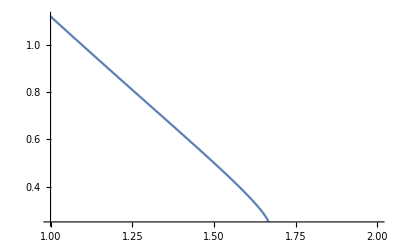

```mathematica
Plot[eqn 18[[2]],{γ,1,2}]
```

```mathematica
eqn 9;
% /.y->0;
Simplify[%];
z^(γ-1)/.Solve[%,z][[1]];
PowerExpand[%];
eqn 20=z^(γ-1)==Collect[%,x];
```

```mathematica
eqn 9;
Limit[%[[1]],γ-> 1]==%[[2]];
eqn 9t=%;
```

```mathematica
{eqn 8,eqn 9t};
%[[2]]/.Solve[%[[1]],z][[1]];
PowerExpand[%];
eqn 14t=%;
```